## Survival probability and Unconditional exit

```mathematica
eq1={s*q1[z]-1==dd*q1''[z],s*q2[z]-1==dd*q2''[z],s*q3[z]-1==dd*q3''[z]};
bc1={q1[0]==0,q3[L]==0,q1'[a]==ⅇ^((μ U)/dd) q2'[a],q3'[b]==ⅇ^((μ U)/dd) q2'[b],q1[a]==q2[a],q2[b]==q3[b]};
sol1=Assuming[0<z<L,DSolve[{eq1,bc1},{q1[z],q2[z],q3[z]},z]];
ql[z_,s_]=q1[z]/.sol1[[1,1]];
qm[z_,s_]=q2[z]/.sol1[[1,2]];
qr[z_,s_]=q3[z]/.sol1[[1,3]];
Q0[z_,s_]=HeavisideTheta[a-z]*ql[z,s]+HeavisideTheta[z-a]*HeavisideTheta[b-z]*qm[z,s]+HeavisideTheta[z-b]*qr[z,s];
Qr[r_,z_,s_]=Q0[z,r+s]/(1-r Q0[z,r+s]);
(*tt[r_,z_]=-SeriesCoefficient[Series[(1-s Qr[r,z,s]),{s,0,2}],1];*)
Subscript[T, 0][z_]=-SeriesCoefficient[Series[(1-s Q0[z,s]),{s,0,2}],1];
Subscript[T, 02][z_]=2*SeriesCoefficient[Series[(1-s Q0[z,s]),{s,0,2}],2];
Subscript[tt, 0][z_,a_,b_,L_,dd_,U_,μ_]=Subscript[T, 0][z];
cv1[z_,a_,b_,L_,dd_,U_,μ_]=√((Subscript[T, 02][z]-(Subscript[T, 0][z])^2)/(Subscript[T, 0][z])^2);
(*Plot[{1,cv1[z,1,4,5,0.5,1.5,0.5]},{z,0,5},PlotRange->{0,2}]*)
tt[r_,z_,a_,b_,L_,dd_,U_,μ_]=-SeriesCoefficient[Series[(1-s Qr[r,z,s]),{s,0,2}],1];
```

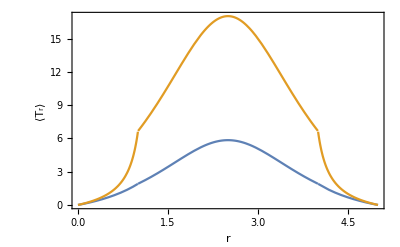

```mathematica
Plot[{tt[1,z,1,4,5,1,0.5,0.5],tt[1,z,1,4,5,1,3.5,0.5]},{z,0,5},Axes->False,Frame->True,FrameLabel->{"r","⟨T_r⟩"}]
```

## Probability density function and Conditional exits

### Regime - I (0<x_0<a) :

```mathematica
eq2={s*p1[x]-DiracDelta[x-z]==dd*p1''[x],s*p2[x]==dd*p2''[x],s*p3[x]==dd*p3''[x]};
bc2={p1[0]==0,p3[L]==0,p1[a]==ⅇ^(-(μ U)/dd) p2[a],p3[b]==ⅇ^(-(μ U)/dd) p2[b],p1'[a]==p2'[a],p2'[b]==p3'[b]};
sol2=DSolve[{eq2,bc2},{p1[x],p2[x],p3[x]},x,Assumptions->{0<z<a<b<L}];
pl[x_,z_,s_]=p1[x]/.sol2[[1,1]];
pm[x_,z_,s_]=p2[x]/.sol2[[1,2]];
pr[x_,z_,s_]=p3[x]/.sol2[[1,3]];
p[x_,z_,s_]=HeavisideTheta[a-x]*pl[x,z,s]+HeavisideTheta[x-a]*HeavisideTheta[b-x]*pm[x,z,s]+HeavisideTheta[x-b]*pr[x,z,s];
pres[x_,z_,s_,r_]=p[x,z,r+s]/(1-r Q0[z,r+s]);
Jminus[z_,s_,r_]=dd*D[pres[x,z,s,r],x]/.x->0;
Jplus[z_,s_,r_]=-dd*D[pres[x,z,s,r],x]/.x->L;
SubMinus[ϵ][z_,r_]=SeriesCoefficient[Series[Jminus[z,s,r],{s,0,2}],0];
SubPlus[ϵ][z_,r_]=SeriesCoefficient[Series[Jplus[z,s,r],{s,0,2}],0];
(*{a,b,L,dd,U,μ}={1,4,5,0.5,1.5,0.5};*)
Plot[{SubPlus[ϵ][0.9,r],SubMinus[ϵ][0.9,r]},{r,0,5},PlotRange->{-0.1,1.1},Frame->True];
SubPlus[T1][r_,z_,a_,b_,L_,dd_,U_,μ_]=-SeriesCoefficient[Series[Jplus[z,s,r],{s,0,2}],1]/SubPlus[ϵ][z,r];
SubMinus[T1][r_,z_,a_,b_,L_,dd_,U_,μ_]=-SeriesCoefficient[Series[Jminus[z,s,r],{s,0,2}],1]/SubMinus[ϵ][z,r];
SubPlus[eps1][r_,z_,a_,b_,L_,dd_,U_,μ_]=SubPlus[ϵ][z,r];
SubMinus[eps1][r_,z_,a_,b_,L_,dd_,U_,μ_]=SubMinus[ϵ][z,r];
```

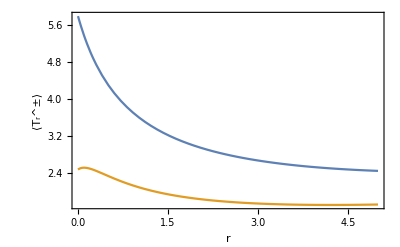

```mathematica
Plot[{SubPlus[T1][r,0.9,1,4,5,1,1.5,0.5],SubMinus[T1][r,0.9,1,4,5,1,1.5,0.5]},{r,0,5},Axes->False,Frame->True,FrameLabel->{"r","⟨T_r^±⟩"}]
```

### Regime - II (a<x_0<b) :

```mathematica
eq2={s*p1[x]==dd*p1''[x],s*p2[x]-DiracDelta[x-z]==dd*p2''[x],s*p3[x]==dd*p3''[x]};
bc2={p1[0]==0,p3[L]==0,p1[a]==ⅇ^(-(μ U)/dd) p2[a],p3[b]==ⅇ^(-(μ U)/dd) p2[b],p1'[a]==p2'[a],p2'[b]==p3'[b]};
sol2=Assuming[0<a<z<b<L,DSolve[{eq2,bc2},{p1[x],p2[x],p3[x]},x]];
pl[x_,z_,s_]=p1[x]/.sol2[[1,1]];
pm[x_,z_,s_]=p2[x]/.sol2[[1,2]];
pr[x_,z_,s_]=p3[x]/.sol2[[1,3]];
p[x_,z_,s_]=HeavisideTheta[a-x]*pl[x,z,s]+HeavisideTheta[x-a]*HeavisideTheta[b-x]*pm[x,z,s]+HeavisideTheta[x-b]*pr[x,z,s];
pres[x_,z_,s_,r_]=p[x,z,r+s]/(1-r Q0[z,r+s]);
Jminus[z_,s_,r_]=dd*D[pres[x,z,s,r],x]/.x->0;
Jplus[z_,s_,r_]=-dd*D[pres[x,z,s,r],x]/.x->L;
SubMinus[ϵ][z_,r_]=SeriesCoefficient[Series[Jminus[z,s,r],{s,0,2}],0];
SubPlus[ϵ][z_,r_]=SeriesCoefficient[Series[Jplus[z,s,r],{s,0,2}],0];
SubPlus[T2][r_,z_,a_,b_,L_,dd_,U_,μ_]=-SeriesCoefficient[Series[Jplus[z,s,r],{s,0,2}],1]/SubPlus[ϵ][z,r];
SubMinus[T2][r_,z_,a_,b_,L_,dd_,U_,μ_]=-SeriesCoefficient[Series[Jminus[z,s,r],{s,0,2}],1]/SubMinus[ϵ][z,r];
SubPlus[eps2][r_,z_,a_,b_,L_,dd_,U_,μ_]=SubPlus[ϵ][z,r];
SubMinus[eps2][r_,z_,a_,b_,L_,dd_,U_,μ_]=SubMinus[ϵ][z,r];
```

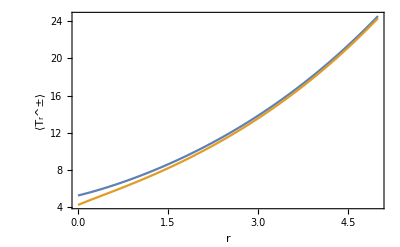

```mathematica
Plot[{SubPlus[T2][r,2.0,1,4,5,1,1.5,0.5],SubMinus[T2][r,2.0,1,4,5,1,1.5,0.5]},{r,0,5},Axes->False,Frame->True,FrameLabel->{"r","⟨T_r^±⟩"}]
```

### Regime - III (b<x_0<l) :

```mathematica
eq2={s*p1[x]==dd*p1''[x],s*p2[x]==dd*p2''[x],s*p3[x]-DiracDelta[x-z]==dd*p3''[x]};
bc2={p1[0]==0,p3[L]==0,p1[a]==ⅇ^(-(μ U)/dd) p2[a],p3[b]==ⅇ^(-(μ U)/dd) p2[b],p1'[a]==p2'[a],p2'[b]==p3'[b]};
sol2=Assuming[0<a<b<z<L,DSolve[{eq2,bc2},{p1[x],p2[x],p3[x]},x]];
pl[x_,z_,s_]=p1[x]/.sol2[[1,1]];
pm[x_,z_,s_]=p2[x]/.sol2[[1,2]];
pr[x_,z_,s_]=p3[x]/.sol2[[1,3]];
p[x_,z_,s_]=HeavisideTheta[a-x]*pl[x,z,s]+HeavisideTheta[x-a]*HeavisideTheta[b-x]*pm[x,z,s]+HeavisideTheta[x-b]*pr[x,z,s];
pres[x_,z_,s_,r_]=p[x,z,r+s]/(1-r Q0[z,r+s]);
Jminus[z_,s_,r_]=dd*D[pres[x,z,s,r],x]/.x->0;
Jplus[z_,s_,r_]=-dd*D[pres[x,z,s,r],x]/.x->L;
SubMinus[ϵ][z_,r_]=SeriesCoefficient[Series[Jminus[z,s,r],{s,0,2}],0];
SubPlus[ϵ][z_,r_]=SeriesCoefficient[Series[Jplus[z,s,r],{s,0,2}],0];
SubPlus[T3][r_,z_,a_,b_,L_,dd_,U_,μ_]=-SeriesCoefficient[Series[Jplus[z,s,r],{s,0,2}],1]/SubPlus[ϵ][z,r];
SubMinus[T3][r_,z_,a_,b_,L_,dd_,U_,μ_]=-SeriesCoefficient[Series[Jminus[z,s,r],{s,0,2}],1]/SubMinus[ϵ][z,r];
SubPlus[eps3][r_,z_,a_,b_,L_,dd_,U_,μ_]=SubPlus[ϵ][z,r];
SubMinus[eps3][r_,z_,a_,b_,L_,dd_,U_,μ_]=SubMinus[ϵ][z,r];
```

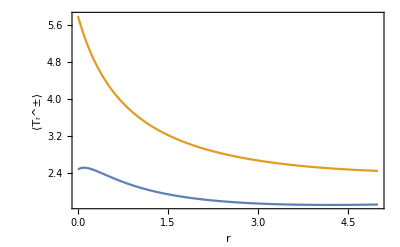

```mathematica
Plot[{SubPlus[T3][r,4.1,1,4,5,1,1.5,0.5],SubMinus[T3][r,4.1,1,4,5,1,1.5,0.5]},{r,0,5},Axes->False,Frame->True,FrameLabel->{"r","⟨T_r^±⟩"}]
```